```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\EG_Ag_MB3\Ag100_allsides\pmf_curve\layer\equilibrate\3_NVT

```mathematica
thermo=Partition[Flatten[Reap[For[i=0,i≤12,i++,
log=OpenRead[StringJoin[ToString[i],"_Restart/thermo.lammps"]];
Find[log,"# Step PotEng"];
thermo=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
Sow[thermo];
];][[2,1]]],12];
```

```mathematica
Length[thermo]
```

64143

```mathematica
TimeSkip=1000;
```

```mathematica
Tavg=Mean[thermo[[All,5]]]
```

299.986

```mathematica
Tstd=StandardDeviation[thermo[[All,5]]]
```

3.4835

```mathematica
Tavg2=Mean[thermo[[TimeSkip;;Length[thermo],5]]]
```

299.983

```mathematica
Tstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],5]]]
```

3.48313

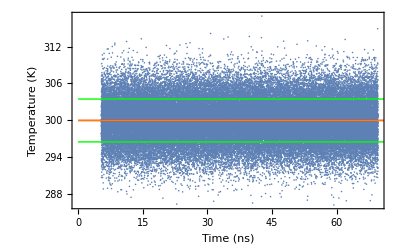

```mathematica
TGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,5]]],2]],Plot[{Tavg,Tavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Tavg2+Tstd2,Tavg2-Tstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Temperature (K)"}]
```

```mathematica
Pavg=Mean[thermo[[All,7]]]
```

-1.17482

```mathematica
Pstd=StandardDeviation[thermo[[All,7]]]
```

874.975

```mathematica
Pavg2=Mean[thermo[[TimeSkip;;Length[thermo],7]]]
```

-2.03726

```mathematica
Pstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],7]]]
```

874.878

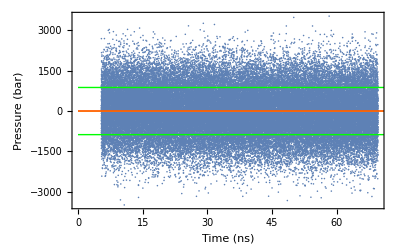

```mathematica
PGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,7]]],2]],Plot[{Pavg,Pavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Pavg2+Pstd2,Pavg2-Pstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Pressure (bar)"}]
```

```mathematica
Volavg=Mean[thermo[[All,6]]]
```

50766.3

```mathematica
Volstd=StandardDeviation[thermo[[All,6]]]
```

5.29185×10^-8

```mathematica
Volavg2=Mean[thermo[[TimeSkip;;Length[thermo],6]]]
```

50766.3

```mathematica
Volstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],6]]]
```

5.23364×10^-8

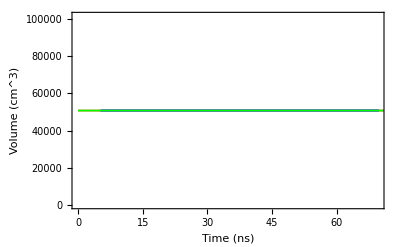

```mathematica
VGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,6]]],2]],Plot[{Volavg,Volavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Volavg2+Volstd2,Volavg2-Volstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Volume (cm^3)"}]
```

```mathematica
Engavg=Mean[thermo[[All,2]]]
```

-2183.87

```mathematica
Engstd=StandardDeviation[thermo[[All,2]]]
```

2.39145

```mathematica
Engavg2=Mean[thermo[[TimeSkip;;Length[thermo],2]]]
```

-2183.86

```mathematica
Engstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],2]]]
```

2.39082

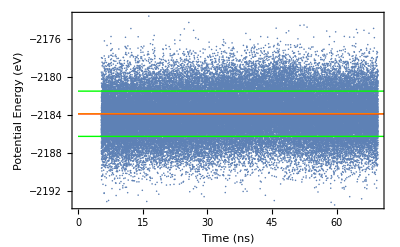

```mathematica
EGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,2]]],2]],Plot[{Engavg,Engavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Engavg2+Engstd2,Engavg2-Engstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Potential Energy (eV)"}]
```

```mathematica
CreateDirectory["graph"];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\EG_Ag_MB3\\Ag100_allsides\\pmf_curve\\layer\\equilibrate\\3_NVT\\graph\\" already exists.

```mathematica
Export["graph/Tgraph.png",TGraph,ImageResolution->300];
Export["graph/Pgraph.png",PGraph,ImageResolution->300];
Export["graph/Vgraph.png",VGraph,ImageResolution->300];
Export["graph/Egraph.png",EGraph,ImageResolution->300];
```

```mathematica
Export["graph/report.txt",{"Tavg:",Tavg," ","Tstd:",Tstd," ","Pavg:",Pavg2," ","Pstd:",Pstd2," ","Volavg:",Volavg2," ","Volstd:",Volstd2," ","PotEngavg:",Engavg2," ","PotEngstd:",Engstd2}]
```

graph/report.txt